```mathematica
Universitatea Tehnică a Moldovei
Facultatea Calculatoare,Informatică și Microelectronică
Specialitatea Tehnologii Informaționale



-Graphics-

Raport
la lucrarea de laborator nr.3
Tema:“Probabilitati”


Disciplina:“Probabilitate si statistica aplicata”
Varianta 3


A efectuat:                              Student TI-231 FR                                             Apareci Aurica
A verificat:                         Asistent universitar            Andrievschi-Bagrin Veronica





Chișinău 2024
```

```mathematica
1. Este dată repartiţia v.a.de tip discre.Se cere:1) să se introducă în Sistemul
Mathematica repartiţia v.a.d.;
2) funcţia de repartiţie şi graficul ei;
3) probabilitatea ca  va lua valori din
intervalul[1,4) 4) valoarea medie 5) dispersia;
6) abaterea medie pătratică
7) momentele iniţiale de
ordine până la 4 inclusiv;
8) momentele centrate de ordine până la 4 inclusiv;
9) asimetria
10) excesul.
```

```mathematica
3) x1=2,x2=1,x3=0,x4=1,p1=0,2,p2=0,4,p3=0,3,p4=0,1;
```

```mathematica
DiscreteDistribution[{-2,-1,3,0},{0.2,0.4,0.3,0.1}]
```

DiscreteDistribution[{-2,-1,3,0},{0.2,0.4,0.3,0.1}]

```mathematica
CDF[DiscreteDistribution[{-2,-1,3,0},{0.2,0.4,0.3,0.1}],x]
```

CDF[DiscreteDistribution[{-2,-1,3,0},{0.2,0.4,0.3,0.1}],x]

```mathematica
Probability[1≤x≤4,x\[Distributed]DiscreteDistribution[{-2,-1,3,0},{0.2,0.4,0.3,0.1}]]
```

Probability[1≤x≤4,x\[Distributed]DiscreteDistribution[{-2,-1,3,0},{0.2,0.4,0.3,0.1}]]

```mathematica
Mean[DiscreteDistribution[{-2,-1,3,0},{0.2,0.4,0.3,0.1}]]
```

```mathematica
Variance[DiscreteDistribution[{-2,-1,3,0},{0.2,0.4,0.3,0.1}]]

StandardDeviation[DiscreteDistribution[{-2,-1,3,0},{0.2,0.4,0.3,0.1}]]
```

```mathematica
Moment[DiscreteDistribution[{-2,-1,3,0},{0.2,0.4,0.3,0.1}],n] for
```

```mathematica
Skewness[DiscreteDistribution[{-2,-1,3,0},{0.2,0.4,0.3,0.1}]]
-Graphics-
```

```mathematica
Kurtosis[DiscreteDistribution[{-2,-1,3,0},{0.2,0.4,0.3,0.1}]]-3
-Graphics-
```

```mathematica
2. Presupunem că probabilitatea statistică că un copil nou născut să fie băiat este egală cu 0.51.Se cere:
1) să se determine repartiţia v.a. care reprezintă numărul de băieţi printre 1000 de copii noi născuţi;
2) să se calculeze probabilitatea că printre 1000 de copii noi născuţi numărul băieţilor va fi cuprims între 300+k
şi 500+k,unde k este numărul variantei.
```

```mathematica
X=BinomialDistribution[1000,0.51]
```

```mathematica
-Graphics-
-Graphics-
```

```mathematica
Probability[300≤X≤500,X\[Distributed]BinomialDistribution[1000,0.51]]
```

```mathematica
3. Numărul  de particule alfa emise de un gram de substanţă radioactivă într-o secundă este o v.a.d.cu
repartiţia Poisson cu parametrul a,unde a este numărul mediu de particule alfa emise într-o secundă.1) Să
se determine seria de repartiţie a v.a.d..2) Să se calculeze probabilităţile evenimentelor:A=într-o
secundă vor fi emise nu mai mult de două particule alfa şi B=într-o secundă vor fi emise cinci particule
alfa,C=într-o secundă vor fi emise mai mult de zece particule alfa.Care este numărul de particule alfa
care corespunde celei mai mari probabilităţi?Să se considere că a=1+0,25n,unde n este numărul variantei.
```

```mathematica
1. Definirea distribuției Poisson
```

```mathematica
ξ=PoissonDistribution[1.75]
-Graphics-
```

```mathematica
2. Determinarea seriei de repartiție
```

```mathematica
PDF[PoissonDistribution[1.75],x]
-Graphics-
```

```mathematica
3. Calculul probabilității pentru evenimentul
A:numărul de particule emise este de cel mult două
Probability[ξ≤2,ξ\[Distributed]PoissonDistribution[1.75]]
-Graphics-
```

```mathematica
4. Calculul probabilității pentru evenimentul
B:numărul de particule emise este exact cinci
```

```mathematica
PDF[PoissonDistribution[1.75],5]
-Graphics-
5. Calculul probabilității pentru evenimentul
C:numărul de particule emise este mai mare de zece
```

```mathematica
Probability[ξ>10,ξ\[Distributed]PoissonDistribution[1.75]]
```

2.39762×10^-6

-Graphics-

```mathematica
6. Determinarea numărului de particule alfa care are cea mai mare probabilitate de a fi emis într-o secundă:
```

```mathematica
Mode[PoissonDistribution[1.75]]
-Graphics-
```

Mode[PoissonDistribution[1.75]]

-Graphics-

```mathematica
4. Să se scrie legea de repartiţie a variabilei aleatoare  care reprezintă numărul de aruncări nereuşite ale unui zar până la prima apariţie a numărului 4. Să se calculeze probabilitatea că numarul aruncărilor nereuşite va varia între 5+k si 15 k unde k este numărul variantei..
```

```mathematica
Sum[(5/6)^i*(1/6),{i,8,18}]
```

122644113671875/609359740010496

```mathematica
5. V.a.c. este definită de densitatea sa de repartiţie f(x).Să se determine:
1) reprezentarea v.a.c. în Sistemul Mathematica
2) linia de repartiţie;
3) funcţia de repartiţie F (x) şi graficul ei,
4)valoarea ei medie;
5) dispersia;6) abaterea medie pătratică;
7) coeficientul de variaţie;
8) momentele iniţiale de ordinele până la 4 inclusiv,
9) momentele centrale de ordinele până la 4 inclusiv;
10) asimetria;
11) excesul;
12) probabilitatea ca  va lua valori din prima jumătate a intervalului de valori posibile.Funcţia f (x) este dată pe variante.
```

```mathematica
f(x)=Piecewise[{{2x-2,1≤x≤2},{0,x<1 or x>2}}]
```

Set::write: Tag Times in f x is Protected.

Piecewise[{{-2+2 x, 1≤x≤2}, {0, True}}]

```mathematica
integrate (2t-2) dt from 1 to x for 1≤x≤2
```

dt for from integrate (-2+2 t) to x≤x≤2

```mathematica
mean of Piecewise[{{2x-2,1≤x≤2},{0,x<1 or x>2}}]
```

```mathematica
variance of Piecewise[{{2x-2,1≤x≤2},{0,x<1 or x>2}}]
```

of variance (Piecewise[{{-2+2 x, 1≤x≤2}, {0, True}}])

```mathematica
standard deviation of Piecewise[{{2x-2,1≤x≤2},{0,x<1 or x>2}}]
```

deviation of standard (Piecewise[{{-2+2 x, 1≤x≤2}, {0, True}}])

```mathematica
moment of Piecewise[{{2x-2,1≤x≤2},{0,x<1 or x>2}}],n
```

```mathematica
Probability of in the First Half of the Interval:
integrate (2x-2) dx from 1 to 1.5
```

First Half in of^2 Probability the^2 (Interval:1.5 dx from integrate to (-2+2 x))

```mathematica
6.V.a. are repartiţia normală cu valoarea medie m şi cu abaterea medie pătratică .1) să se instaleze pachetul de programe Statistics`NormalDistribution`;2) să se definească (introducă) v.a.c.dată;3) să se definească (determine) densitatea de repartiţie;4) să se construiască linia de repartiţie;5) să se definească (determine) funcţia de repartiţie;6) să se construiască graficul funcţiei de repartiţie;7) să se construiască pe acelaşi desen graficele densităţii de repartiţie şi al funcţiei de repartiţie;8) să se construiască pe acelaş desen gfaficele densităţii de repartiţie şi al funcţiei de repartiţie astfel ca grosimea graficului densităţii de repartiţie să fie egală cu 0,5 din grosimea standard,iar grosimea graficului funcţiei de repartiţie să fie egală cu 0,9 din grosimea standard;9) Să se calculeze probabilitatea ca  să ia valori din intervalul[,].Valorile lui m,  şi  sunt date pe variante.
```

```mathematica
Definirea variabilei aleatoare cu distribuție normală:
```

```mathematica
dist=NormalDistribution[5,2]
```

NormalDistribution[5,2]

```mathematica
pdf=PDF[dist,x]
```

(ⅇ^(-1/8 (-5+x)^2))/(2 √(2 π))

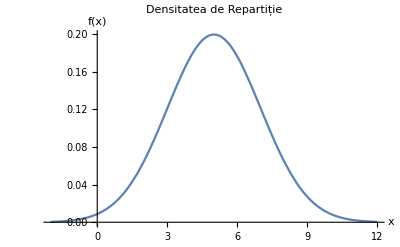

```mathematica
Plot[pdf,{x,-2,12},PlotLabel->"Densitatea de Repartiție",AxesLabel->{"x","f(x)"}]
```

```mathematica
cdf=CDF[dist,x]
```

1/2 Erfc[(5-x)/(2 √2)]

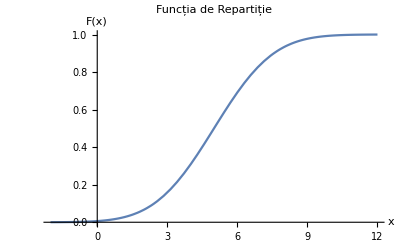

```mathematica
Plot[cdf,{x,-2,12},PlotLabel->"Funcția de Repartiție",AxesLabel->{"x","F(x)"}]
```

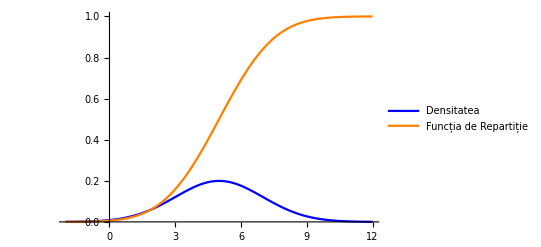

```mathematica
Plot[{pdf,cdf},{x,-2,12},PlotStyle->{Blue,Orange},PlotLegends->{"Densitatea","Funcția de Repartiție"}]
```

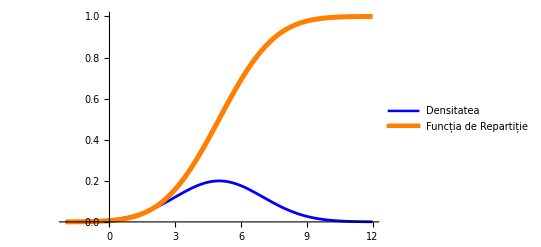

```mathematica
Plot[{pdf,cdf},{x,-2,12},PlotStyle->{Directive[Blue,Thickness[0.005]],Directive[Orange,Thickness[0.009]]},PlotLegends->{"Densitatea","Funcția de Repartiție"}]
```

```mathematica
probability=NProbability[2≤x≤6,x\[Distributed]dist]
```

0.624655

```mathematica
probability=cdf/.x->6-(cdf/.x->2)
```

1/2 Erfc[(-1+1/2 Erfc[3/(2 √2)])/(2 √2)]

```mathematica
7. Înălţimea unui bărbat este o v.a.cu repartiţia normală.Presupunem că această repartiţie are parametrii m=175+(-1)n /n cm şi =6-(-1)n
/n cm.Să se formeze programul de conficţionate a costumelor bărbăteşti pentru o fabrică de confecţii care se referă la asigurarea cu costume a bărbaţilor,înălţimile cărora aparţin intervalelor:[150,155),[155,160),[160,165),[165,170),[170,175),[175,180),[180,185),[185,190),[190,195),[195,200] n fiind numarul variantei,n=1…30.
```

```mathematica
(*Definirea intervalelor*)intervale={{150,155},{155,160},{160,165},{165,170},{170,175},{175,180},{180,185},{185,190},{190,195},{195,200}};

(*Functie care calculeaza probabilitatea pentru fiecare interval dat n*)
probabilitatiPentruN[n_]:=Module[{m,sigma,dist,probabilitati},m=175+(-1)^n/n;
sigma=6-(-1)^n/n;
dist=NormalDistribution[m,sigma];
probabilitati=Table[CDF[dist,interval[[2]]]-CDF[dist,interval[[1]]],{interval,intervale}];
probabilitati]

(*Calculul probabilităților pentru un exemplu de variantă,de exemplu n=1*)
probabilitatiPentruN[1]
```

{1/2 Erfc[19/(7 √2)]-1/2 Erfc[(12 √2)/7],-1/2 Erfc[19/(7 √2)]+Erfc[√2]/2,1/2 Erfc[9/(7 √2)]-Erfc[√2]/2,-1/2 Erfc[9/(7 √2)]+1/2 Erfc[(2 √2)/7],1/2 Erfc[-1/(7 √2)]-1/2 Erfc[(2 √2)/7],-1/2 Erfc[-1/(7 √2)]+1/2 Erfc[-(3 √2)/7],1/2 Erfc[-11/(7 √2)]-1/2 Erfc[-(3 √2)/7],-1/2 Erfc[-11/(7 √2)]+1/2 Erfc[-(8 √2)/7],1/2 Erfc[-3/(√2)]-1/2 Erfc[-(8 √2)/7],-1/2 Erfc[-3/(√2)]+1/2 Erfc[-(13 √2)/7]}

```mathematica
8. Presupunem că o convorbire telefonică durează în medie 5 minute şi este o v.a. de repartiţie exponenţială.1) Să se introducă în Sistemul Mathematica d.r.a v.a.c..2) Să se determine funcţia de
repartiţie şi să se construiască graficul ei.3) Dacă vă apropriaţi de o cabină telefonică imediat după ce o persoană a întrat în ea atunci care este probabilitatea că o să aşteptaţi nu mai mult de 2+n/3 minute,unde n
este numărul variantei,n=1,2,…,30?
```

```mathematica
lambda=1/5;(*Parametrul ratei pentru media de 5 minute*)X=ExponentialDistribution[lambda];
```

```mathematica
CDF_X[t_]:=CDF[X,t]
Plot[CDF_X[t],{t,0,20},PlotRange->{0,1},PlotLabel->"Funcția de repartiție pentru convorbire telefonică"]
waitTime=2+3/3;(*Valoarea 2+n/3*)probabilityWait=CDF[X,waitTime]
```

SetDelayed::write: Tag ExponentialDistribution in (CDF:Blank[ExponentialDistribution[1/5]])[t_] is Protected.

$Failed

-Graphics-

1-1/ⅇ^(3/5)

```mathematica
9. Un autobuz circulă regulat cu intervalul 30 minute.1) Să se scrie în Sistemul Mathematica d.r.a v.a.c. care reprezintă durata aşteptării autobuzului de către un pasager care soseste în staţie într-un moment aleator de timp.2) Să se construiască linia de repartiţie.3) Să se determine f.r.e şi să se construiască graficul ei.4) Care este probabilitatea că sosind în staţie pasagerul va aştepta autobuzul nu mai mult de 10+n/2 minute unde numărul n coincide cu numărul variantei.
```

```mathematica
Definirea variabilei aleatoare
X=UniformDistribution[{0,30}];
```

```mathematica
Construirea liniei de repartiție:
```

```mathematica
CDF_X[t_]:=CDF[X,t]
Plot[CDF_X[t],{t,0,30},PlotRange->{0,1},PlotLabel->"Linia de repartiție pentru așteptarea autobuzului"]
```

SetDelayed::write: Tag UniformDistribution in (CDF:Blank[UniformDistribution[{0,30}]])[t_] is Protected.

$Failed

-Graphics-

```mathematica
Determinarea funcției de densitate de probabilitate (f.r.e) și construirea graficului acesteia:
PDF_X[t_]:=PDF[X,t]
Plot[PDF_X[t],{t,0,30},PlotLabel->"Funcția de densitate pentru așteptarea autobuzului"]
```

SetDelayed::write: Tag Times in construirea de de densitate Determinarea funcției graficului și probabilitate f.r.e (acesteia:(PDF:Blank[UniformDistribution[{0,30}]])[t_]) is Protected.

$Failed

-Graphics-

```mathematica
Calculul probabilității
```

```mathematica
waitTime=10+3/2;
probabilityWait=CDF[X,waitTime]
```

23/60

```mathematica
10. Cantitatea anuală de precipitaţii atmosferice are repartiţie normală.Presupunem că anual,cantitatea de precipitaţii într o anumită regiune este o v.a.aleatoare de repartiţie normală de parametrii m=500 (mm)şi  150. Care este probabilitatea că în anul viitor cantitatea de precipitaţii va fi cuprinsă între 400+5n şi 500+5n,unde n este numărul variantei.Dacă considerăm că un an este secetos când cantitatea de precipitaţii nu depăşeşte 300 mm,atunci care este probabilitatea că doi din viitorii zece ani vor fi secetoşi?
```

```mathematica
Definirea variabilei aleatoare
```

```mathematica
mu=500;sigma=150;
X=NormalDistribution[mu,sigma];
Calculul probabilității
lowerBound=400+5*3;upperBound=500+5*3;probabilityRange=CDF[X,upperBound]-CDF[X,lowerBound]
```

Calculul probabilității

1/2 Erfc[-1/(10 √2)]-1/2 Erfc[17/(30 √2)]

```mathematica
Calculul probabilități
```

```mathematica
droughtProbability=CDF[X,300];(*Probabilitatea ca un an să fie secetos*)probabilityTwoDroughtYears=BinomialDistribution[10,droughtProbability]
Probability[x==2,x\[Distributed]probabilityTwoDroughtYears]
```

BinomialDistribution[10,1/2 Erfc[(2 √2)/3]]

(45 (-1+Erf[(2 √2)/3])^2 (1+Erf[(2 √2)/3])^8)/1024